```mathematica
rawdata=Import["/Users/stevenschowalter/Desktop/phys191mms/Rb Data/428fstep7.txt","Data"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

80

```mathematica
freq=Take[rawdata,All,{1}];
signal=Take[rawdata,All,{2}];
```

```mathematica
plotdata=Take[rawdata,All,2];
```

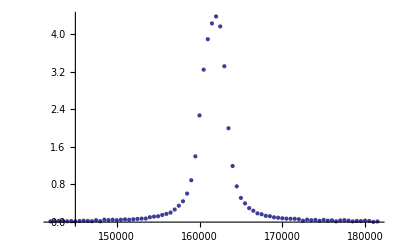

```mathematica
dataplot=ListPlot[plotdata,PlotRange->All]
```

```mathematica
Do[If[Max[signal]==signal[[i]][[1]],{Print[i,plotdata[[i]]],{max}=freq[[i]]}],{i,1,num}]
```

41{162000.,4.371}

```mathematica
model=g/(π (g^2+(x-x0)^2/b));
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
fitdata=NonlinearRegress[plotdata,model,{x0,g,b},x,MaxIterations->1000]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.36417×10^-17, -3.08448×10^-12, -3.08448×10^-12}, {0., « 1 », -« 23 »}, {0., 0., -« 24 »}} may contain significant numerical errors.

{BestFitParameters→{x0→6.30949×10^6,g→83.352,b→83.352},ParameterCITable→ | Estimate | Asymptotic SE | CI
x0 | 6.30949×10^6 | 4.38017×10^21 | {-8.72204×10^21,8.72204×10^21}
g | 83.352 | 3.87585×10^24 | {-7.71781×10^24,7.71781×10^24}
b | 83.352 | 3.87585×10^24 | {-7.71781×10^24,7.71781×10^24},EstimatedVariance→1.3813,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 3 | 4.48772×10^-9 | 1.49591×10^-9
Error | 77 | 106.36 | 1.3813
Uncorrected Total | 80 | 106.36 | 
Corrected Total | 79 | 87.9779 | ,AsymptoticCorrelationMatrix→(1. | -1. | 1.
-1. | 1. | -1.
1. | -1. | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 1.46927×10^21
Max Parameter-Effects | 3.31238×10^36
95. % Confidence Region | 0.605967}

```mathematica
fit=model/.fitdata[[1]][[2]];
```

```mathematica
fitplot=Plot[fit,{x,100000,200000},PlotStyle->{Red, Thick}];
```

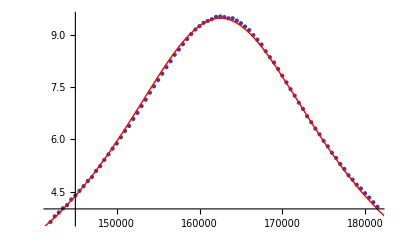

```mathematica
Show[dataplot,fitplot]
```